```mathematica
(*2D point*)
```

```mathematica
pt = {_ , _};
```

```mathematica
(*half space*)
```

```mathematica
halfSpace = hP[pt , pt] | hPC[pt , pt];
```

```mathematica
(*expression is a sum of intersections*)
```

```mathematica
subsetExpr = sumE[{halfSpace..}...];
```

```mathematica
(**)
```

```mathematica
sum[a:subsetExpr , b:subsetExpr]:= sumE@@Join[List@@a , List@@b];
```

```mathematica
intersection[a:subsetExpr , b:subsetExpr]:=sumE@@Outer[Join,List@@a , List@@b , 1][[1]];
```

```mathematica
gr[e:subsetExpr]:=(List@@e)/.hP[a_ , b_]:> {Dotted , InfiniteLine[{a , b}]};
```

```mathematica
in[p:pt , hP[a_ , b_]]:=(Join[(p-a) , {0}]×Join[(b-a),{0}])[[3]]<=0;
```

```mathematica
in[p:pt , hPC[a_ , b_]]:=(Join[(p-a) , {0}]×Join[(b-a),{0}])[[3]]<0;
```

```mathematica
in[p:pt , x:subsetExpr]:= Or@@(Function[xs , And@@(in[p , #]&/@xs)]/@x);
```

```mathematica
(*example*)
```

```mathematica
polyA=sumE[{hP[{3,0} , {0 , 3}],hP[{0,3} , {-3 , 0}],hP[{-3,0},{0,-3}],hP[{0 , -3} , {3 , 0}]}];
```

```mathematica
polyB=sumE[{hP[{1 , 0}+{3,0} , {1 , 0}+{0 , 3}],hP[{1 , 0}+{0,3} , {1 , 0}+{-3 , 0}],hP[{1 , 0}+{-3,0},{1 , 0}+{0,-3}],hP[{1 , 0}+{0 , -3} , {1 , 0}+{3 , 0}]}];
```

```mathematica
polyC=sumE[{hP[{0 , -0.7}+{3,0} , {0 , -0.7}+{0 , 3}],hP[{0 , -0.7}+{0,3} , {0 , -0.7}+{-3 , 0}],hP[{0 , -0.7}+{-3,0},{0 , -0.7}+{0,-3}],hP[{0 , -0.7}+{0 , -3} , {0 , -0.7}+{3 , 0}]}];
```

```mathematica
plt = sum[intersection[polyA , polyB] , polyC]
```

sumE[{hP[{3,0},{0,3}],hP[{0,3},{-3,0}],hP[{-3,0},{0,-3}],hP[{0,-3},{3,0}],hP[{4,0},{1,3}],hP[{1,3},{-2,0}],hP[{-2,0},{1,-3}],hP[{1,-3},{4,0}]},{hP[{3,-0.7},{0,2.3}],hP[{0,2.3},{-3,-0.7}],hP[{-3,-0.7},{0,-3.7}],hP[{0,-3.7},{3,-0.7}]}]

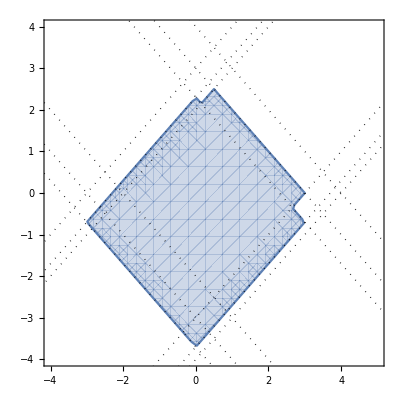

```mathematica
Show[RegionPlot[in[{x , y} , plt] , {x , -4,5} , {y , -4 , 4}],Graphics[gr[plt] , Axes->True]]
```

```mathematica
(*czy odcinek[{r1 , r2} , h = (hP[] | hpC[])] należy do bryły x: *)
```

```mathematica
(*1 - czy r1 oraz r2 należą do x?*)
```

```mathematica
(*2 - czy h należy do x?*)
```

```mathematica
(*Jeżeli 1 oraz 2 to odcinek należy do x.*)
```

```mathematica
(*conjugate[odcinek[{r1 , r2} , hP[{a , b}]]] = odcinek[{r1 , r2} , hPC[{a , b}]]*)
```

```mathematica
(*conjugate[odcinek[{r1 , r2} , hPC[{a , b}]]] = odcinek[{r1 , r2} , hP[{a , b}]]*)
```

```mathematica
(*Kiedy odcinek jest zewnętrzną krawędzią x?*)
```

```mathematica
(*odcinek[{r1 , r2} , hP[{a , b}]] ∈ x oraz conjugate[odcinek[{r1 , r2} , hP[{a , b}]]] ∉ x*)
```

```mathematica
(*trojkat1 = h1∩h2∩h2*)
```

```mathematica
(*trojkat1^* = conjugate[h1]∪conjugate[h2]∪conjugate[h2]*)
```